## 2D Moire pattern of Kagome and Hexagonal lattice:

#### The parameters that you can change is the twist angle, lattice constant, the atom radius (maybe there will be two kind atoms)

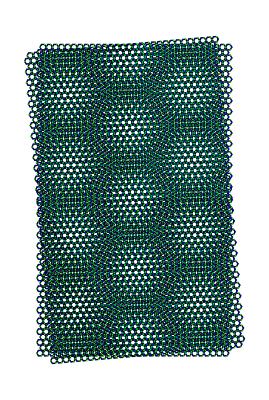

```mathematica
(*Moire Kagome lattice*)
Clear["Global`*"]
hexagonal[center_,a_]:=Table[{First@center+a*Cos[i*π/3],Last@center+a*Sin[i*π/3]},{i,0,6,1}];

hexagonal`plot[center_,a_,r1_,r2_]:=Module[{sites},sites=hexagonal[center,a];
h`sites=Table[sites[[i]],{i,1,Length@sites,2}];
b`sites=Table[sites[[i]],{i,2,Length@sites,2}];Graphics[{Line[sites],Blue,AbsolutePointSize[r1],Point[h`sites],Green,AbsolutePointSize[r2],Point[b`sites]}]];
Kagome[size_,a_,r_]:=Module[{width=Abs[First@size],length=Abs[Last@size]},gx=2a;gy=2a*Sin[π/3];
nx=Floor[width/gx];ny=Floor[length/gy];
centers`first=Table[{i*gx,2*j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`second=Table[{gx/2+i*gx,gy+2*j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`first=Flatten[centers`first,1];
centers`second=Flatten[centers`second,1];
centers=Join[centers`first,centers`second];
Show[Table[hexagonal`plot[centers[[i]],a,First@r,Last@r],{i,Length@centers}],PlotRange->All]];
Hexagonal[size_,a_,r_]:=Module[{width=Abs[First@size],length=Abs[Last@size]},gx=3a;gy=2a*Sin[π/3];
nx=Floor[width/gx];ny=Floor[length/gy];
centers`first=Table[{i*gx,j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`second=Table[{gx/2+i*gx,gy/2+j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`first=Flatten[centers`first,1];
centers`second=Flatten[centers`second,1];
centers=Join[centers`first,centers`second];
Show[Table[hexagonal`plot[centers[[i]],a,First@r,Last@r],{i,Length@centers}],PlotRange->All]];
Moire`kagome`pattern[w_,l_,twist`angle_,a_,r_]:=Show[{Kagome[{w,l},a,r],Graphics[Rotate[First@Kagome[{w,l},a,r],twist`angle,{w/2,l/2}]]}];
Moire`hexagonal`pattern[w_,l_,twist`angle_,a_,r_]:=Show[{Hexagonal[{w,l},a,r],Graphics[Rotate[First@Hexagonal[{w,l},a,r],twist`angle,{w/2,l/2}]]}];
(*Change Parameters here*)
(*twist angle*)twist`angle=5Degree;
(*lattice constant*) a=5; width=300;length=500;
(*atom radius*)r1=1;r2=1;
Moire`kagome`pattern[width,length,twist`angle,a,{r1,r2}]
```

## 3D Moire lattice of Kagome and Hexagonal lattice:

```mathematica
Clear["Global`*"]
hexagonal[center_,z_,a_]:=Table[{First@center+a*Cos[i*π/3],Last@center+a*Sin[i*π/3],z},{i,0,6,1}];

hexagonal`plot[center_,z_,a_,r1_,r2_]:=Module[{sites},sites=hexagonal[center,z,a];
h`sites=Table[sites[[i]],{i,1,Length@sites,2}];
b`sites=Table[sites[[i]],{i,2,Length@sites,2}];Graphics3D[{Line[sites],Blue,Ball[h`sites,r1],Green,Ball[b`sites,r2]},Boxed->False,ViewPoint->Top,ImageSize->Large]];
Kagome[size_,z_,a_,r_]:=Module[{width=Abs[First@size],length=Abs[Last@size]},gx=2a;gy=2a*Sin[π/3];
nx=Floor[width/gx];ny=Floor[length/gy];
centers`first=Table[{i*gx,2*j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`second=Table[{gx/2+i*gx,gy+2*j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`first=Flatten[centers`first,1];
centers`second=Flatten[centers`second,1];
centers=Join[centers`first,centers`second];
Show[Table[hexagonal`plot[centers[[i]],z,a,First@r,Last@r],{i,Length@centers}],PlotRange->All]];
Hexagonal[size_,z_,a_,r_]:=Module[{width=Abs[First@size],length=Abs[Last@size]},gx=3a;gy=2a*Sin[π/3];
nx=Floor[width/gx];ny=Floor[length/gy];
centers`first=Table[{i*gx,j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`second=Table[{gx/2+i*gx,gy/2+j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`first=Flatten[centers`first,1];
centers`second=Flatten[centers`second,1];
centers=Join[centers`first,centers`second];
Show[Table[hexagonal`plot[centers[[i]],z,a,First@r,Last@r],{i,Length@centers}],PlotRange->All]];
Moire`hexagonal`lattice[w_,l_,twist`angle_,z_,a_,r_]:=Show[{Hexagonal[{w,l},0,a,r],Graphics3D[Rotate[First@Hexagonal[{w,l},z,a,r],twist`angle,{0,0,1},{w/2,l/2,z}]]}];
Moire`kagome`lattice[w_,l_,twist`angle_,z_,a_,r_]:=Show[{Kagome[{w,l},0,a,r],Graphics3D[Rotate[First@Kagome[{w,l},z,a,r],twist`angle,{0,0,1},{w/2,l/2,z}]]}];

(*twist angle*)twist`angle=10Degree;
(*lattice constant*) a=5; width=500;length=500;
(*atom radius*)r1=1.1;r2=1;
(*layers` interval*)z=10r1;
Moire`hexagonal`lattice[width,length,twist`angle,z,a,{r1,r2}];
Moire`kagome`lattice[width,length,twist`angle,z,a,{r1,r2}]
```

-Graphics3D-

## TMD materials’s 3D moire lattice-2H phase

```mathematica
Clear["Global`*"]
hexagonal[center_,z_,a_]:=Table[{First@center+a*Cos[i*π/3],Last@center+a*Sin[i*π/3],z},{i,0,6,1}];

hexagonal`plot`two`H[center_,z_,deltaz_,a_,r1_,r2_]:=Module[{sites,sites`center},sites`center=hexagonal[center,z,a];
h`sites=Table[sites`center[[i]],{i,1,Length@sites`center,2}];
h`sites=Drop[h`sites,-1];
sites`up=hexagonal[center,z+deltaz,a];
b`up`sites=Table[sites`up[[i]],{i,2,Length@sites`up,2}];
sites`down=hexagonal[center,z-deltaz,a];
b`down`sites=Table[sites`down[[i]],{i,2,Length@sites`down,2}];
lines={};
AppendTo[lines,Table[{h`sites[[i]],b`up`sites[[j]]},{i,Length@h`sites},{j,Length@b`up`sites}]];

AppendTo[lines,Table[{h`sites[[i]],b`down`sites[[j]]},{i,Length@h`sites},{j,Length@b`down`sites}]];
lines=Flatten[lines,2];
line`for`plot=Delete[lines,{{2},{6},{7},{11},{15},{16}}];
Graphics3D[{Line@line`for`plot,Blue,Ball[h`sites,r1],Green,Ball[b`up`sites,r2],Green,Ball[b`down`sites,r2]},Boxed->False,ViewPoint->Top,ImageSize->Large]];
hexagonal`plot`one`T[center_,z_,deltaz_,a_,r1_,r2_]:=Module[{sites},sites`center=hexagonal[center,z,a];sites`down=hexagonal[center,z-deltaz,a];up`center={First@center,Last@center,z+deltaz};
h`sites=Table[sites`down[[i]],{i,1,Length@sites`center,2}];
b`sites=Table[sites`center[[i]],{i,2,Length@sites`down,2}];
h`sites=Drop[h`sites,-1];
AppendTo[h`sites,up`center];
lines={};
AppendTo[lines,Table[{h`sites[[i]],b`sites[[j]]},{i,Length@h`sites},{j,Length@b`sites}]];
lines=Flatten[lines,2];
line`for`plot=Delete[lines,{{2},{6},{7}}];
b`sites=Drop[b`sites,-1];
Graphics3D[{Line[line`for`plot],Green,Ball[h`sites,r1],Blue,Ball[b`sites,r2],Red,Ball[up`center,r2]},Boxed->False,ViewPoint->Top,ImageSize->Large]];
(*Choose 1T or 2H phase here*)
hexagonal`plot[center_,z_,deltaz_,a_,r1_,r2_]:=hexagonal`plot`one`T[center,z,deltaz,a,r1,r2];

Hexagonal[size_,z_,deltaz_,a_,r_]:=Module[{width=Abs[First@size],length=Abs[Last@size]},gx=3a;gy=2a*Sin[π/3];
nx=Floor[width/gx];ny=Floor[length/gy];
centers`first=Table[{i*gx,j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`second=Table[{gx/2+i*gx,gy/2+j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`first=Flatten[centers`first,1];
centers`second=Flatten[centers`second,1];
centers=Join[centers`first,centers`second];
Show[Table[hexagonal`plot[centers[[i]],z,deltaz,a,First@r,Last@r],{i,Length@centers}],PlotRange->All]];
Moire`TMD`lattice[w_,l_,twist`angle_,z_,deltaz_,a_,r_]:=Show[{Hexagonal[{w,l},0,deltaz,a,r],Graphics3D[Rotate[First@Hexagonal[{w,l},z,deltaz,a,r],twist`angle,{0,0,1},{w/2,l/2,z}]]}];
(*twist angle*)twist`angle=30Degree;
(*lattice constant*) a=2; width=100;length=200;
(*atom radius*)r1=0.5;r2=0.3;
(*layers` interval*)z=10r1;deltaz=3r1;
Hexagonal[{10,20},z,deltaz,a,{r1,r2}]
Moire`TMD`lattice[width,length,twist`angle,z,deltaz,a,{r1,r2}]
```

```mathematica
Clear["Global`*"]
hexagonal[center_,z_,a_]:=Table[{First@center+a*Cos[i*π/3],Last@center+a*Sin[i*π/3],z},{i,0,6,1}];

hexagonal`plot[center_,z_,deltaz_,a_,r1_,r2_]:=Module[{sites},sites`center=hexagonal[center,z,a];sites`down=hexagonal[center,z-deltaz,a];up`center={First@center,Last@center,z+deltaz};
h`sites=Table[sites`down[[i]],{i,1,Length@sites`center,2}];
b`sites=Table[sites`center[[i]],{i,2,Length@sites`down,2}];
h`sites=Drop[h`sites,-1];
AppendTo[h`sites,up`center];
lines={};
AppendTo[lines,Table[{h`sites[[i]],b`sites[[j]]},{i,Length@h`sites},{j,Length@b`sites}]];
lines=Flatten[lines,2];
line`for`plot=Delete[lines,{{2},{6},{7}}];
b`sites=Drop[b`sites,-1];
Graphics3D[{Line[line`for`plot],Green,Ball[h`sites,r1],Blue,Ball[b`sites,r2],Red,Ball[up`center,r2]},Boxed->False,ViewPoint->Top,ImageSize->Large]];
Hexagonal[size_,z_,deltaz_,a_,r_]:=Module[{width=Abs[First@size],length=Abs[Last@size]},gx=3a;gy=2a*Sin[π/3];
nx=Floor[width/gx];ny=Floor[length/gy];
centers`first=Table[{i*gx,j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`second=Table[{gx/2+i*gx,gy/2+j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`first=Flatten[centers`first,1];
centers`second=Flatten[centers`second,1];
centers=Join[centers`first,centers`second];
Show[Table[hexagonal`plot[centers[[i]],z,deltaz,a,First@r,Last@r],{i,Length@centers}],PlotRange->All]];
Moire`TMD`lattice[w_,l_,twist`angle_,z_,deltaz_,a_,r_]:=Show[{Hexagonal[{w,l},0,deltaz,a,r],Graphics3D[Rotate[First@Hexagonal[{w,l},z,deltaz,a,r],twist`angle,{0,0,1},{w/2,l/2,z}]]}];
(*twist angle*)twist`angle=10Degree;
(*lattice constant*) a=2; width=100;length=200;
(*atom radius*)r1=0.3;r2=0.3;
(*layers` interval*)z=10r1;deltaz=3r1;
Hexagonal[{20,20},z,deltaz,a,{r1,r2}]
Moire`TMD`lattice[width,length,twist`angle,z,deltaz,a,{r1,r2}]
```

-Graphics3D-

-Graphics3D-

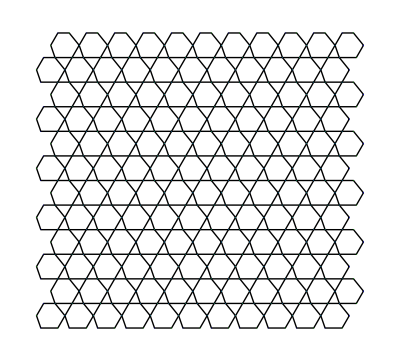

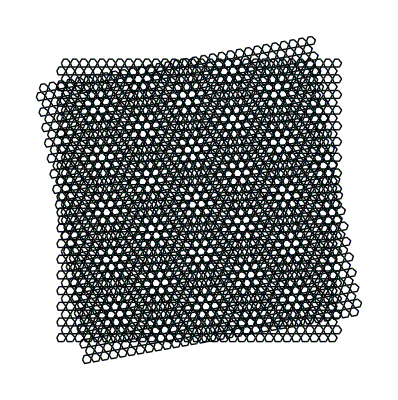

```mathematica
(*Moire Kagome lattice*)
Clear["Global`*"]
hexagonal[center_,a_]:=Module[{sites},sites=Table[{First@center+a*Cos[i*π/3],Last@center+a*Sin[i*π/3]},{i,0,6,1}];sites[[1]]={First@center+a+a/5,Last@center};sites[[4]]={First@center-a+a/5,Last@center};
sites[[3]]={First@sites[[3]]+a/5,Last@sites[[3]]};
sites[[6]]={First@sites[[6]]+a/5,Last@sites[[6]]};
sites[[-1]]={First@center+a+a/5,Last@center};sites];

hexagonal`plot[center_,a_,r1_,r2_]:=Module[{sites},sites=hexagonal[center,a];
h`sites=Table[sites[[i]],{i,1,Length@sites,2}];
b`sites=Table[sites[[i]],{i,2,Length@sites,2}];Graphics[{Line[sites],Blue,AbsolutePointSize[r1],Point[h`sites],Green,AbsolutePointSize[r2],Point[b`sites]}]];

Kagome[size_,a_,r_]:=Module[{width=Abs[First@size],length=Abs[Last@size]},gx=2a;gy=2a*Sin[π/3];
nx=Floor[width/gx];ny=Floor[length/gy];
centers`first=Table[{i*gx,2*j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`second=Table[{gx/2+i*gx,gy+2*j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`first=Flatten[centers`first,1];
centers`second=Flatten[centers`second,1];
centers=Join[centers`first,centers`second];
Show[Table[hexagonal`plot[centers[[i]],a,First@r,Last@r],{i,Length@centers}],PlotRange->All]];


Hexagonal[size_,a_,r_]:=Module[{width=Abs[First@size],length=Abs[Last@size]},gx=3a;gy=2a*Sin[π/3];
nx=Floor[width/gx];ny=Floor[length/gy];
centers`first=Table[{i*gx,j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`second=Table[{gx/2+i*gx,gy/2+j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`first=Flatten[centers`first,1];
centers`second=Flatten[centers`second,1];
centers=Join[centers`first,centers`second];
Show[Table[hexagonal`plot[centers[[i]],a,First@r,Last@r],{i,Length@centers}],PlotRange->All]];
Moire`kagome`pattern[w_,l_,twist`angle_,a_,r_]:=Show[{Kagome[{w,l},a,r],Graphics[Rotate[First@Kagome[{w,l},a,r],twist`angle,{w/2,l/2}]]}];
Moire`hexagonal`pattern[w_,l_,twist`angle_,a_,r_]:=Show[{Hexagonal[{w,l},a,r],Graphics[Rotate[First@Hexagonal[{w,l},a,r],twist`angle,{w/2,l/2}]]}];
(*Change Parameters here*)
(*twist angle*)twist`angle=10Degree;
(*lattice constant*) a=5; width=300;length=300;
(*atom radius*)r1=0;r2=0;
Kagome[{100,100},5,{0,0}]
Moire`kagome`pattern[width,length,twist`angle,a,{r1,r2}]
```

```mathematica
Clear["Global`*"]
hexagonal[center_,z_,a_]:=Table[{First@center+a*Cos[i*π/3],Last@center+a*Sin[i*π/3],z},{i,0,6,1}];

hexagonal`plot[center_,z_,deltaz_,a_,r1_,r2_]:=Module[{sites},sites`center=hexagonal[center,z,a];sites`down=hexagonal[center,z-deltaz,a];up`center={First@center,Last@center,z+deltaz};
h`sites=Table[sites`down[[i]],{i,1,Length@sites`center,2}];
b`sites=Table[sites`center[[i]],{i,2,Length@sites`down,2}];
h`sites=Drop[h`sites,-1];
AppendTo[h`sites,up`center];
lines={};
AppendTo[lines,Table[{h`sites[[i]],b`sites[[j]]},{i,Length@h`sites},{j,Length@b`sites}]];
lines=Flatten[lines,2];
line`for`plot=Delete[lines,{{2},{6},{7}}];
b`sites=Drop[b`sites,-1];
Graphics3D[{Line[line`for`plot],Green,Ball[h`sites,r1],Blue,Ball[b`sites,r2],Red,Ball[up`center,r2]},Boxed->False,ViewPoint->Top,ImageSize->Large]];
hexagonal`plot[{0,0},0,0.1,0.5,0.01,0.03];
Hexagonal[size_,z_,deltaz_,a_,r_]:=Module[{width=Abs[First@size],length=Abs[Last@size]},gx=3a;gy=2a*Sin[π/3];
nx=Floor[width/gx];ny=Floor[length/gy];
centers`first=Table[{i*gx,j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`second=Table[{gx/2+i*gx,gy/2+j*gy},{i,0,nx,1},{j,0,ny/2,1}];
centers`first=Flatten[centers`first,1];
centers`second=Flatten[centers`second,1];
centers=Join[centers`first,centers`second];
Show[Table[hexagonal`plot[centers[[i]],z,deltaz,a,First@r,Last@r],{i,Length@centers}],PlotRange->All]];
Moire`TMD`lattice[w_,l_,twist`angle_,z_,deltaz_,a_,r_]:=Show[{Hexagonal[{w,l},0,deltaz,a,r],Graphics3D[Rotate[First@Hexagonal[{w,l},z,deltaz,a,r],twist`angle,{0,0,1},{w/2,l/2,z}]]}];
(*twist angle*)twist`angle=10Degree;
(*lattice constant*) a=2; width=100;length=200;
(*atom radius*)r1=0.3;r2=0.3;
(*layers` interval*)z=10r1;deltaz=3r1;
Hexagonal[{20,20},z,deltaz,a,{r1,r2}]
Moire`TMD`lattice[width,length,twist`angle,z,deltaz,a,{r1,r2}]
```

-Graphics3D-

-Graphics3D-